81+144 x0^4+350 x0^2 x1^2+144 x1^4-225 (x0^2+x1^2)

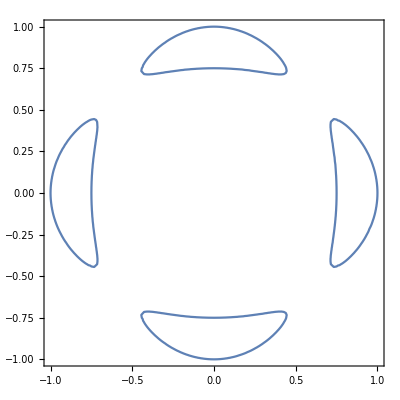

144 x0^4+350 x0^2 x1^2+144 x1^4-225 x0^2 x2^2-225 x1^2 x2^2+81 x2^4

144*x0^4 + 350*x0^2*x1^2 + 144*x1^4 - 225*x0^2*x2^2 - 225*x1^2*x2^2 + 81*x2^4

```mathematica
f = 144 x0^4 + 144 x1^4 - 225(x0^2 + x1^2) + 350 x0^2x1^2 + 81
ContourPlot[{f == 0} ,{x0,-1,1},{x1,-1,1}]

h= ResourceFunction["PolynomialHomogenize"][Expand[f],{x0, x1},x2]
h //InputForm
```

200278673408-595460201600 u0^2+693929621376 u0^4-405749476800 u0^6+124963617024 u0^8-19096446600 u0^10+1134213192 u0^12-595460201600 u1^2+1320961032200 u0^2 u1^2-1023241679100 u0^4 u1^2+318272542650 u0^6 u1^2-23234924925 u0^8 u1^2-4187394225 u0^10 u1^2+693929621376 u1^4-1023241679100 u0^2 u1^4+413794479582 u0^4 u1^4-36573182775 u0^6 u1^4-2846712924 u0^8 u1^4-405749476800 u1^6+318272542650 u0^2 u1^6-36573182775 u0^4 u1^6+17459149050 u0^6 u1^6+124963617024 u1^8-23234924925 u0^2 u1^8-2846712924 u0^4 u1^8-19096446600 u1^10-4187394225 u0^2 u1^10+1134213192 u1^12

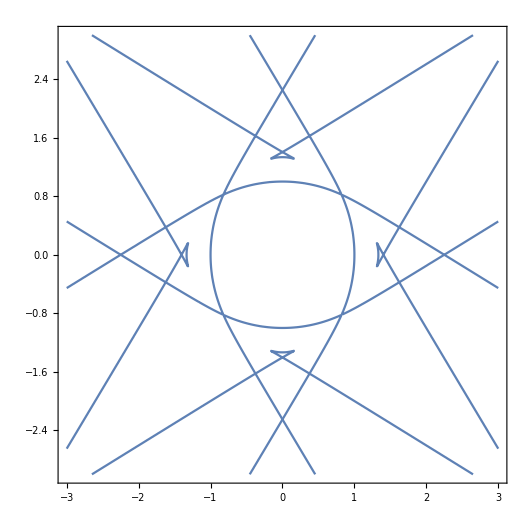

```mathematica
d = 1134213192*u0^12-4187394225*u0^10*u1^2-2846712924*u0^8*u1^4+17459149050*u0^6*u1^6-2846712924*u0^4*u1^8-4187394225*u0^2*u1^10+1134213192*u1^12-19096446600*u0^10*u2^2-23234924925*u0^8*u1^2*u2^2-36573182775*u0^6*u1^4*u2^2-36573182775*u0^4*u1^6*u2^2-23234924925*u0^2*u1^8*u2^2-19096446600*u1^10*u2^2+124963617024*u0^8*u2^4+318272542650*u0^6*u1^2*u2^4+413794479582*u0^4*u1^4*u2^4+318272542650*u0^2*u1^6*u2^4+124963617024*u1^8*u2^4-405749476800*u0^6*u2^6-1023241679100*u0^4*u1^2*u2^6-1023241679100*u0^2*u1^4*u2^6-405749476800*u1^6*u2^6+693929621376*u0^4*u2^8+1320961032200*u0^2*u1^2*u2^8+693929621376*u1^4*u2^8-595460201600*u0^2*u2^10-595460201600*u1^2*u2^10+200278673408*u2^12;
s = d /. u2-> 1
ContourPlot[s == 0, {u0, -3, 3}, {u1, -3, 3},MaxRecursion->2, PlotPoints->100]
```